# “Hump-backed plateau”

Make sure you set the pathpackage below to your current package directory

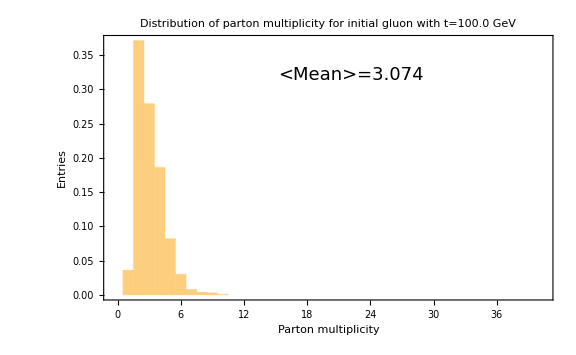
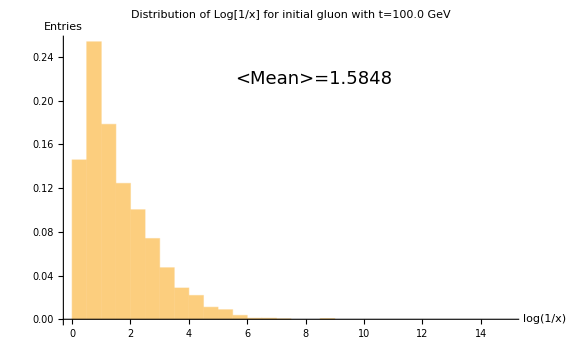
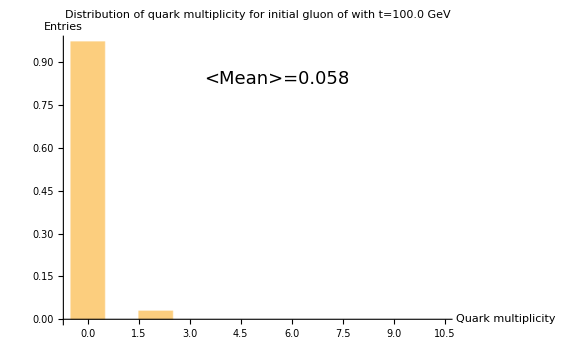

```mathematica
pathpackage="/Users/gianmicheleinnocenti/Desktop/parton-shower-simulator";
Clear[kernelpath,notebookpath];
kernelpath = StringJoin[pathpackage,"/Kernel"];
resultspath = StringJoin[pathpackage,"/Notebooks/plots"];
pathmain = StringJoin[kernelpath,"/PartonShowerMCFull.wl"]
SetDirectory[kernelpath];
<<"PartonShowerMCFull.wl"
SilentErrors[];
SetStandardSeeds[];
resultspath = StringJoin[pathpackage,"/Notebooks/plots/plotsNTonlygtogg_"];
vactivatedebug = 0;
vnevents = 1000;
vtscaleptinit =100.;
vtscalecutoff = 1.;
vmaxiteration = 200; (* just a satefy tool to avoid infinite loops, value is not meaningful*)
vactivateqqbar = 1;
veffectivemassquark = 1.5;
RunShowerMulti[vnevents,vtscaleptinit,vtscalecutoff,SudakovPgtoggvacuumNT,SudakovPgtoqqbarvacuumLT,PgtoggvacuumNT,PgtoqqbarvacuumLT,PgtoggvacuumNTsymmetric,PgtoqqbarvacuumLTsymmetric,
                               vactivatedebug,vmaxiteration,vactivateqqbar,veffectivemassquark,resultspath]
```